```mathematica
<<RiemannHilbert`
```

## Auto routine function

```mathematica
ScaledRHSolver[{scs_,gs_,gms_}]:=Module[{standardf,pts,R,Uls,z0,sc,Cus,uz0,usc,us,gl,lsGs},
standardf=Fun[IdentityMatrix[2]&,Sequence@@##]&/@gms;
pts=standardf//Points;
R=RHSolver[standardf];

Function[x,
Uls={};
Function[ls,
{{z0,sc},lsGs}=ls;
Cus=(Dot@@#)&/@Thread[
Function[uls,
{uz0,usc,us}=uls;
FromValueList[standardf,Cauchy[us,((z0+pts/sc)-uz0)usc]//ToMatrixOfLists//Flatten]//AddIdentityMatrix
]/@Uls
];
gl=Fun[Function[z,#⟦1⟧[x,z0+z/sc]],Sequence@@#⟦2⟧]&/@Thread[{lsGs,gms}];
If[Cus=={},
Uls=Join[{{z0,sc,R[gl]}},Uls],
Uls=Join[{{z0,sc,R[#⟦1⟧.#⟦2⟧.Inverse[#⟦1⟧]&/@Thread[{Cus,gl}]]}},Uls]];
]/@Thread[{scs[x]//Transpose,gs//Transpose}];
(-(DomainIntegrate[#⟦3⟧]⟦1,2⟧)/(2π I #⟦2⟧)&/@Uls)//Total]
]
```

## HM

```mathematica
α=0;
σ=-1;
s[1]=Exp[-I π σ(α+1/2)];
s[2]=0;
s[3]=Exp[I π σ(α+1/2)];
{s[4],s[5],s[6]}=-Array[s,3];

S[k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[k_?OddQ]:=({{1, 0}, {s[k], 1}});

β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[y_,λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[y_,λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[y_,λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
ν=σ α/2;
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[y_,z_]:=Y[y,z].MatrixExp[(-g[y,z]) σ3];
Φp[y_,z_]:=Yp[y,z].MatrixExp[-(gp[y,z]) σ3];
Φm[y_,z_]:=Ym[y,z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG];
GGΣ[_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[y_,z_]=Φm[y,z].Inverse[S[1]].Inverse[Φm[y,z]]//Simplify;
GGΣin[y_,z_]=GGΣ[y,z]//Inverse;
GG[_][_,_?InfinityQ]:=IdentityMatrix[2];
GG[6][y_,z_]=Φ[y,z].S[6].Inverse[Φ[y,z]]//Simplify;
GG[1][y_,z_]=Φ[y,z].S[1].Inverse[Φ[y,z]]//Simplify;
GG[3][y_,z_]=Φ[y,z].S[3].Inverse[Φ[y,z]]//Simplify;
GG[4][y_,z_]=Φ[y,z].S[4].Inverse[Φ[y,z]]//Simplify;
```

```mathematica
GLC[1][y_,z_]=Inverse[Φm[y,z]];
GLC[2][y_,z_]=S[6].S[1].S[3].Inverse[Φ[y,z]];
GLC[3][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
```

```mathematica
GRC[1][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
GRC[2][y_,z_]=S[6].Inverse[Φ[y,z]];
GRC[3][y_,z_]=Inverse[Φm[y,z]];
```

```mathematica
rngg={.5,2.3};

Cdefs[n_]:={({{-#, #}, {#, -#}})&,({{GGΣ, GGΣin}, {GG[3], GG[6]}, {GG[4], GG[1]}, {GLC[1], GRC[1]}, {GLC[2], GRC[2]}, {GLC[3], GRC[3]}}),({{Line[{.5,3.}], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})};
```

```mathematica
slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];
```

```mathematica
DomainIntegrate[slv[20][Sqrt[10./2]]]
```

{{-0.0393146+9.29395×10^-14 ⅈ,6.76685×10^-14-0.000882185 ⅈ},{5.76861×10^-14-0.000882184 ⅈ,0.0393146+1.19949×10^-13 ⅈ}}

```mathematica
data=Partition[ReadList["RiemannHilbert/Data/McLeodSolution.txt",Number],7];
```

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;
```

```mathematica
PainleveIIHM[n_,x_]:=2 ΦθSeries[x]-1/(π I) DomainIntegrate[slv[n][Sqrt[-x/2]]]⟦1,2⟧
```

```mathematica
data⟦1,1⟧
```

-40.

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.24306,-4.99999+6.83098×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.13712,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{1.73495,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,-50.]//Timing
```

{0.863311,-4.99999-5.77348×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,data⟦1,1⟧]-data⟦1,3⟧
```

6.24096×10^-11-2.84424×10^-15 ⅈ

```mathematica
PainleveIIHM[30,data⟦1,1⟧]-data⟦1,3⟧
```

-9.59233×10^-14+5.77175×10^-15 ⅈ

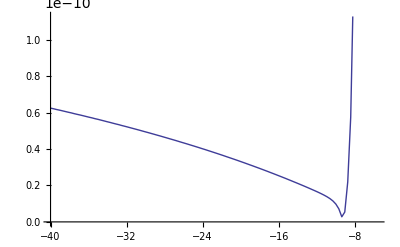

```mathematica
Monitor[ListLinePlot[Table[{data⟦k,1⟧,p[data⟦k,1⟧]-data⟦k,3⟧//Abs},{k,1,551,5}]],k]
```

## HM Tests

```mathematica
α=0;
σ=-1;
s[1]=Exp[-I π σ(α+1/2)];
s[2]=0;
s[3]=Exp[I π σ(α+1/2)];
{s[4],s[5],s[6]}=-Array[s,3];

S[k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[k_?OddQ]:=({{1, 0}, {s[k], 1}});

β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[y_,λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[y_,λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[y_,λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
ν=σ α/2;
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[y_,z_]:=Y[y,z].MatrixExp[(-g[y,z]) σ3];
Φp[y_,z_]:=Yp[y,z].MatrixExp[-(gp[y,z]) σ3];
Φm[y_,z_]:=Ym[y,z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG];
GGΣ[_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[y_,z_]=Φm[y,z].Inverse[S[1]].Inverse[Φm[y,z]]//Simplify;
GGΣin[y_,z_]=GGΣ[y,z]//Inverse;
GG[_][_,_?InfinityQ]:=IdentityMatrix[2];
GG[6][y_,z_]=Φ[y,z].S[6].Inverse[Φ[y,z]]//Simplify;
GG[1][y_,z_]=Φ[y,z].S[1].Inverse[Φ[y,z]]//Simplify;
GG[3][y_,z_]=Φ[y,z].S[3].Inverse[Φ[y,z]]//Simplify;
GG[4][y_,z_]=Φ[y,z].S[4].Inverse[Φ[y,z]]//Simplify;
```

```mathematica
GLC[1][y_,z_]=Inverse[Φm[y,z]];
GLC[2][y_,z_]=S[6].S[1].S[3].Inverse[Φ[y,z]];
GLC[3][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
```

```mathematica
GRC[1][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
GRC[2][y_,z_]=S[6].Inverse[Φ[y,z]];
GRC[3][y_,z_]=Inverse[Φm[y,z]];
```

```mathematica
rngg={.5,3.};

Cdefs[n_]:={({{-#, #}, {#, -#}})&,({{GGΣ, GGΣin}, {GG[3], GG[6]}, {GG[4], GG[1]}, {GLC[1], GRC[1]}, {GLC[2], GRC[2]}, {GLC[3], GRC[3]}}),({{Line[rngg], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})};
```

```mathematica
slv//Clear;slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];
```

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;
```

```mathematica
PainleveIIHM[n_,x_]:=2 ΦθSeries[x]-1/(π I) DomainIntegrate[slv[n][Sqrt[-x/2]]]⟦1,2⟧
```

```mathematica
pv=With[{n=50,x=-5.},-1/(π I) DomainIntegrate[slv[n][Sqrt[-x/2]]]⟦1,2⟧]
```

0.00165505+1.99282×10^-15 ⅈ

```mathematica
2 ΦθSeries[-5.]+ pv
```

-1.57948+1.99282×10^-15 ⅈ

```mathematica
G=ConstructCurve[Cdefs[40],Sqrt[6./2]];
```

```mathematica
With[{n=40,x=-5.},DomainIntegrate[slv[n][Sqrt[-x/2]]]]
```

```mathematica
{{-0.07933883162221163-5.681219383824043*^-17 ⅈ,-4.0592529337857286*^-16-0.005199485199131456 ⅈ},{-1.272419669628988*^-15-0.005199485199126622 ⅈ,0.07933883162221098+9.62771529167128*^-16 ⅈ}}
```

```mathematica
G//RHSolve//DomainIntegrate
```

```mathematica
{{-0.07933883162221163-5.681219383824043*^-17 ⅈ,-4.0592529337857286*^-16-0.005199485199131456 ⅈ},{-1.272419669628988*^-15-0.005199485199126622 ⅈ,0.07933883162221098+9.62771529167128*^-16 ⅈ}} -{{-0.07933883162221261-2.108122704180815*^-15 ⅈ,1.4051260155412137*^-15-0.005199485199130344 ⅈ},{7.051650929845721*^-16-0.005199485199129649 ⅈ,0.07933883162221142+3.7643499428696714*^-16 ⅈ}}
```

{{9.85323×10^-16+2.05131×10^-15 ⅈ,-1.81105×10^-15-1.11196×10^-15 ⅈ},{-1.97758×10^-15+3.02709×10^-15 ⅈ,-4.44089×10^-16+5.86337×10^-16 ⅈ}}

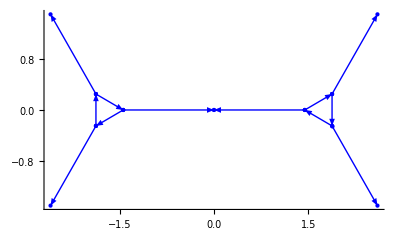

```mathematica
G//DomainPlot
```

```mathematica
G⟦1⟧//Last
```

{{0.999975,5.04551×10^-6-0.0000247179 ⅈ},{-5.04551×10^-6-0.0000247179 ⅈ,1.00003}}

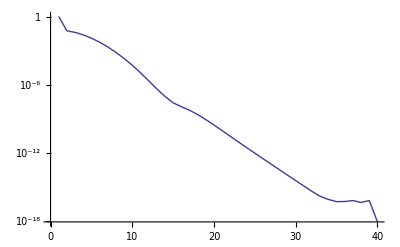
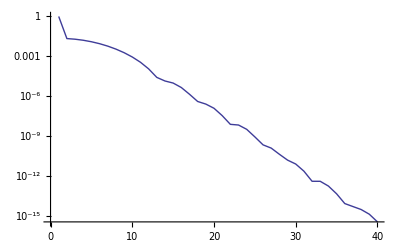
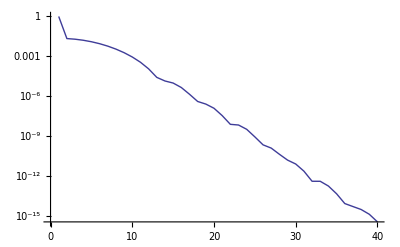
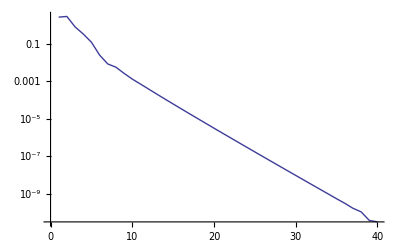
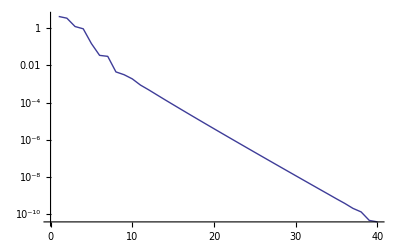
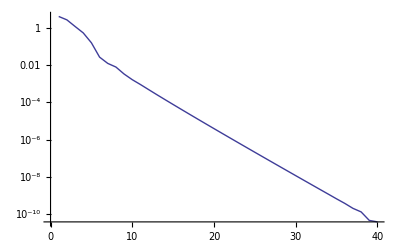
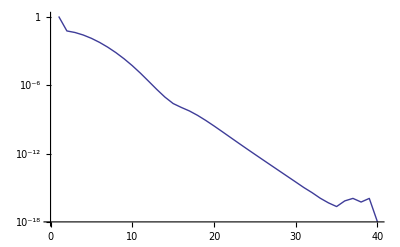
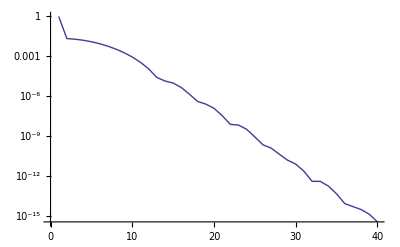
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@G
```

```mathematica
.
```

```mathematica
2 ΦθSeries[-5.]
```

```mathematica
-1.5811388300841898
```

```mathematica
PainleveIIHM[60,-7.]
```

```mathematica
-1.870137278580925+4.351175501724395*^-16 ⅈ
```

```mathematica
Select[data,First[#]==-20.&]⟦1,3⟧-PainleveIIHM[50,-20.]
```

1.01092×10^-10-2.39439×10^-15 ⅈ

```mathematica
Select[data,First[#]==-10.&]⟦1,3⟧-PainleveIIHM[50,-10.]
```

3.96081×10^-9+2.17697×10^-15 ⅈ

```mathematica
Select[data,First[#]==-7.&]⟦1,3⟧-PainleveIIHM[50,-7.]
```

8.56608×10^-8-1.75704×10^-15 ⅈ

```mathematica
{{-7.,9.080303779394358,-1.870137275910715,0.1338819675687076,2.206107647934002,0.6260118377500663,-2.010796706237386}}
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
-1.731025435933375-1.520702707074744*^-15 ⅈ
```

```mathematica
-1.731024958831779
```

```mathematica
-1.579490393158594+1.846488690071875*^-15 ⅈ
```

```mathematica
-1.579483782542241+1.992816292604485*^-15 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422612+6.90224540248159*^-16 ⅈ
```

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
Select[data,First[#]==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-5.,5.622378711823955,-1.579487087847008,0.1589913778691818,1.726754832688724,0.4571001663908862,-1.838905305470106}}
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[200,{-I,0.,I},-6.]
```

```mathematica
1.7310249641825814-6.51404263862787*^-10 ⅈ
```

```mathematica
1.5794870876539058+1.1152572199080169*^-9 ⅈ
```

```mathematica
1.5794856393446206-2.758557826609831*^-9 ⅈ
```

```mathematica
1.5794812822096675+2.9161579817582606*^-9 ⅈ
```

```mathematica
1.5794812863147345-5.184634943589117*^-10 ⅈ
```

```mathematica
1.5794812816197141-2.9485036634468997*^-10 ⅈ
```

```mathematica
1.5794812802206075+1.0231815394945443*^-12 ⅈ
```

```mathematica
1.5794812664580633+2.9692515113310947*^-10 ⅈ
```

```mathematica
PainleveII[{-I,0,I},-4.9999999]
```

```mathematica
1.5794870697048897+2.7642776956327*^-10 ⅈ
```

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.24306,-4.99999+6.83098×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.13712,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{1.73495,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,-50.]//Timing
```

{0.863311,-4.99999-5.77348×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,data⟦1,1⟧]-data⟦1,3⟧
```

6.24096×10^-11-2.84424×10^-15 ⅈ

```mathematica
PainleveIIHM[30,data⟦1,1⟧]-data⟦1,3⟧
```

-9.59233×10^-14+5.77175×10^-15 ⅈ

```mathematica
Monitor[ListLinePlot[Table[{data⟦k,1⟧,p[data⟦k,1⟧]-data⟦k,3⟧//Abs},{k,1,551,5}]],k]
```

-Graphics-

## s2

```mathematica
α=0;
σ=-1;
s[1]=Exp[-I π σ(α+1/2)];
s[2]=0;
s[3]=Exp[I π σ(α+1/2)];
{s[4],s[5],s[6]}=-Array[s,3];

S[k_?EvenQ]:=({{1, s[k]}, {0, 1}});
S[k_?OddQ]:=({{1, 0}, {s[k], 1}});

β[y_,λ_]:=((λ-y)/(λ+y))^(1/4);
βp[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,0];
βm[y_,λ_]:=PowerBranch[(λ-y)/(λ+y),1/4,-2π];
Y[y_,λ_]:=1/2({{β[y,λ]+β[y,λ]^(-1), -σ (β[y,λ]-β[y,λ]^(-1))}, {-σ (β[y,λ]-β[y,λ]^(-1)), β[y,λ]+β[y,λ]^(-1)}});
Yp[y_,λ_]:=1/2({{βp[y,λ]+βp[y,λ]^(-1), -σ (βp[y,λ]-βp[y,λ]^(-1))}, {-σ (βp[y,λ]-βp[y,λ]^(-1)), βp[y,λ]+βp[y,λ]^(-1)}});
Ym[y_,λ_]:=1/2({{βm[y,λ]+βm[y,λ]^(-1), -σ (βm[y,λ]-βm[y,λ]^(-1))}, {-σ (βm[y,λ]-βm[y,λ]^(-1)), βm[y,λ]+βm[y,λ]^(-1)}});
ν=σ α/2;
σ3=({{1, 0}, {0, -1}});
Σ=({{0, I}, {I, 0}});

g[_,_?InfinityQ]:=∞;
g[y_,z_]:=I 4/3 (z+y)^(3/2)(z-y)^(3/2);
gp[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,0];
gm[y_,z_]:=I 4/3 (z+y)^(3/2)PowerBranch[z-y,3/2,-2π];
θ[x_,z_]:=4 I/3z^3+I x z;
Φ[y_,z_]:=Y[y,z].MatrixExp[(-g[y,z]) σ3];
Φp[y_,z_]:=Yp[y,z].MatrixExp[-(gp[y,z]) σ3];
Φm[y_,z_]:=Ym[y,z].MatrixExp[-(gm[y,z]) σ3];
```

```mathematica
Clear[GGΣ,GGΣin,GG];
GGΣ[_,_?InfinityQ]:=IdentityMatrix[2];
GGΣ[y_,z_]=Φm[y,z].Inverse[S[1]].Inverse[Φm[y,z]]//Simplify;
GGΣin[y_,z_]=GGΣ[y,z]//Inverse;
GG[_][_,_?InfinityQ]:=IdentityMatrix[2];
GG[6][y_,z_]=Φ[y,z].S[6].Inverse[Φ[y,z]]//Simplify;
GG[1][y_,z_]=Φ[y,z].S[1].Inverse[Φ[y,z]]//Simplify;
GG[3][y_,z_]=Φ[y,z].S[3].Inverse[Φ[y,z]]//Simplify;
GG[4][y_,z_]=Φ[y,z].S[4].Inverse[Φ[y,z]]//Simplify;
```

```mathematica
GLC[1][y_,z_]=Inverse[Φm[y,z]];
GLC[2][y_,z_]=S[6].S[1].S[3].Inverse[Φ[y,z]];
GLC[3][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
```

```mathematica
GRC[1][y_,z_]=S[6].S[1].Inverse[Φp[y,z]];
GRC[2][y_,z_]=S[6].Inverse[Φ[y,z]];
GRC[3][y_,z_]=Inverse[Φm[y,z]];
```

```mathematica
rngg={.5,3.};

Cdefs[n_]:={({{-#, #}, {#, -#}})&,({{GGΣ, GGΣin}, {GG[3], GG[6]}, {GG[4], GG[1]}, {GLC[1], GRC[1]}, {GLC[2], GRC[2]}, {GLC[3], GRC[3]}}),({{Line[rngg], n}, {Line[Exp[2 I π/3]rngg], n}, {Line[Exp[-2I π/3]rngg], n}, {Line[{1 ,Exp[-2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[-2I π/3] ,Exp[2I π/3] }rngg⟦1⟧], n}, {Line[{Exp[2I π/3] ,1 }rngg⟦1⟧], n}})};
```

```mathematica
slv//Clear;slv[n_]:=slv[n]=ScaledRHSolver[Cdefs[n]];
```

```mathematica
ΦθSeries[x_]:=-Sqrt[-x/2]/2 ;
```

```mathematica
PainleveIIHM[n_,x_]:=2 ΦθSeries[x]-1/(π I) DomainIntegrate[slv[n][Sqrt[-x/2]]]⟦1,2⟧
```

```mathematica
PainleveIIHM[60,-6.]
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
Select[data,#⟦1⟧==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-7.,9.080303779394358,-1.870137275910715,0.1338819675687076,2.206107647934002,0.6260118377500663,-2.010796706237386}}
```

```mathematica
-1.7310249588317774-7.324662821113464*^-16 ⅈ
```

```mathematica
-1.731025435933375-1.520702707074744*^-15 ⅈ
```

```mathematica
-1.731024958831779
```

```mathematica
-1.579490393158594+1.846488690071875*^-15 ⅈ
```

```mathematica
-1.579483782542241+1.992816292604485*^-15 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.2921003393445538*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422399-1.5930382388927512*^-16 ⅈ
```

```mathematica
-1.5794837825422612+6.90224540248159*^-16 ⅈ
```

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
Select[data,First[#]==-6.&]
```

```mathematica
{{-6.,7.278816139236562,-1.731024958831779,0.1447782842572886,1.984968230748079,0.5487136948259861,-1.932551780876071}}
```

```mathematica
{{-5.,5.622378711823955,-1.579487087847008,0.1589913778691818,1.726754832688724,0.4571001663908862,-1.838905305470106}}
```

```mathematica
RiemannHilbert`Painleve`II`Private`PainleveIISmall[200,{-I,0.,I},-6.]
```

```mathematica
1.7310249641825814-6.51404263862787*^-10 ⅈ
```

```mathematica
1.5794870876539058+1.1152572199080169*^-9 ⅈ
```

```mathematica
1.5794856393446206-2.758557826609831*^-9 ⅈ
```

```mathematica
1.5794812822096675+2.9161579817582606*^-9 ⅈ
```

```mathematica
1.5794812863147345-5.184634943589117*^-10 ⅈ
```

```mathematica
1.5794812816197141-2.9485036634468997*^-10 ⅈ
```

```mathematica
1.5794812802206075+1.0231815394945443*^-12 ⅈ
```

```mathematica
1.5794812664580633+2.9692515113310947*^-10 ⅈ
```

```mathematica
PainleveII[{-I,0,I},-4.9999999]
```

```mathematica
1.5794870697048897+2.7642776956327*^-10 ⅈ
```

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.24306,-4.99999+6.83098×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{5.13712,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[30,-50.]//Timing
```

{1.73495,-4.99999+6.81738×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,-50.]//Timing
```

{0.863311,-4.99999-5.77348×10^-15 ⅈ}

```mathematica
PainleveIIHM[20,data⟦1,1⟧]-data⟦1,3⟧
```

6.24096×10^-11-2.84424×10^-15 ⅈ

```mathematica
PainleveIIHM[30,data⟦1,1⟧]-data⟦1,3⟧
```

-9.59233×10^-14+5.77175×10^-15 ⅈ

```mathematica
Monitor[ListLinePlot[Table[{data⟦k,1⟧,p[data⟦k,1⟧]-data⟦k,3⟧//Abs},{k,1,551,5}]],k]
```

-Graphics-